```mathematica
(* What we expect for variance of 2 cos(2 pi k x / N ) *)
```

```mathematica
f[k_] =1/2 1/(4 Pi k) (1 - Exp[- 2 Pi k] );
```

### Martingale data : N = 512, interval size = 512, 100 samples k = 4

```mathematica
M4 = {-0.0169727+I*(-0.0498521),-0.0668631+I*(-0.0874006),-0.0507715+I*(-0.0200628),-0.0673782+I*(-0.000334775),-0.0619127+I*(0.0403497),0.00570017+I*(0.0344381),-0.0148254+I*(0.045351),-0.0439953+I*(0.00635656),-0.0835452+I*(0.0230116),-0.100386+I*(0.0420669),-0.136527+I*(-0.00133638),-0.0957414+I*(-0.040899),0.0166026+I*(-0.0673314),-0.000550219+I*(-0.107278),-0.0208533+I*(-0.0740863),-0.0300119+I*(-0.0439745),-0.0482472+I*(-0.0160083),-0.00399681+I*(0.0207401),-0.0333272+I*(0.0329829),-0.0144502+I*(0.0651223),0.0195966+I*(0.103376),0.0219462+I*(0.0781639),-0.00315435+I*(0.0665428),0.0382467+I*(0.0875992),0.0104263+I*(0.118714),0.0408938+I*(0.12899),0.0879718+I*(-0.0281427),0.00595367+I*(0.0251439),0.0215239+I*(0.068104),0.0380189+I*(0.0453297),0.04988+I*(0.00877282),0.051274+I*(-0.063227),0.0810876+I*(-0.079762),0.0361313+I*(-0.0894683),0.0369759+I*(-0.111643),0.0155655+I*(-0.0652797),0.0871264+I*(-0.0237497),0.0747486+I*(-0.0321908),0.0143454+I*(-0.0158993),0.00461759+I*(-0.052611),0.0286965+I*(-0.119707),0.0475334+I*(-0.130234),0.13034+I*(-0.0868554),0.179841+I*(-0.0574281),0.229871+I*(-0.0415443),0.222733+I*(-0.0791987),0.20594+I*(-0.15397),0.227428+I*(-0.114489),0.236931+I*(-0.0780017),0.114806+I*(-0.153004),0.0179447+I*(-0.192772),0.0195817+I*(-0.21362),0.0248124+I*(-0.228976),0.00786568+I*(-0.335433),0.0186188+I*(-0.277272),0.0511201+I*(-0.256293),0.0266959+I*(-0.179117),-0.0794962+I*(-0.176063),-0.0957516+I*(-0.168963),-0.0842044+I*(-0.199376),-0.179789+I*(-0.155999),-0.105539+I*(-0.104507),-0.0770985+I*(-0.103519),-0.0858382+I*(-0.131746),-0.0506653+I*(-0.113441),-0.0306458+I*(-0.120124),0.0476081+I*(-0.0951472),0.0246454+I*(-0.0997034),0.0375193+I*(-0.0614477),0.0144454+I*(0.00675072),-0.00362988+I*(-0.0512398),-0.0217787+I*(-0.143386),-0.0251727+I*(-0.153796),-0.0627126+I*(-0.122181),-0.0240891+I*(-0.164232),-0.0802659+I*(-0.180576),-0.0335429+I*(-0.196385),-0.0612222+I*(-0.182541),-0.0783958+I*(-0.155761),-0.106483+I*(-0.152803),-0.147059+I*(-0.0612912),-0.131908+I*(-0.0563396),-0.125546+I*(-0.11399),-0.0954075+I*(-0.139003),-0.0964179+I*(-0.116576),-0.0730959+I*(-0.132911),-0.0972791+I*(-0.12081),-0.144651+I*(-0.0644118),-0.157242+I*(-0.107607),-0.148021+I*(-0.0886845),-0.094702+I*(-0.1378),-0.0460377+I*(-0.178144),-0.0422323+I*(-0.100924),0.0280622+I*(-0.0718684),0.0243405+I*(-0.115406),0.0845521+I*(-0.0762489),0.126224+I*(-0.12868),0.114607+I*(-0.166168),0.0922922+I*(-0.173063),0.0261339+I*(-0.186793)};
```

### Analysis

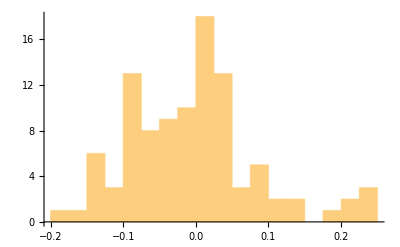

```mathematica
Histogram[Re[M4], {.025}]
```

```mathematica
de4 = HistogramDistribution[Re[M4]];
```

```mathematica
Moment[de4, 2]
f[4.]/2
```

0.00763333

0.00497359

### Martingale data : N = 512, interval size = 5 * 512, 100 samples k = 4

```mathematica
M4again = {-0.033548+I*(-0.0296528),0.00165616+I*(0.0670618),-0.170434+I*(-0.00864872),-0.12315+I*(-0.00569908),-0.112676+I*(0.00115171),-0.169438+I*(-0.0102714),-0.189238+I*(-0.0125708),-0.0822378+I*(-0.0921104),-0.138265+I*(-0.0955812),-0.157459+I*(-0.254587),-0.00718595+I*(-0.229318),-0.0805631+I*(-0.0873674),0.139258+I*(-0.155544),-0.036369+I*(-0.116695),-0.0949324+I*(-0.153612),-0.00482502+I*(-0.0556259),0.21368+I*(-0.115764),0.151888+I*(-0.155003),0.143756+I*(-0.212732),-0.115556+I*(-0.165625),0.062027+I*(-0.036175),0.0196014+I*(-0.153615),0.0541317+I*(0.0328215),-0.0227012+I*(0.130541),0.0425233+I*(0.116976),0.0673235+I*(0.0739667),0.0690463+I*(0.112513),-0.0204989+I*(0.00945991),0.0288423+I*(0.00280398),0.0660503+I*(0.00661509),-0.000673117+I*(-0.0908157),0.0109238+I*(-0.0465209),0.025862+I*(-0.12182),0.102957+I*(-0.00241368),0.237457+I*(0.0136062),0.165231+I*(-0.057449),0.121874+I*(-0.166252),-0.0638371+I*(-0.104394),-0.0897079+I*(0.0647838),-0.0241774+I*(0.127786),-0.0279506+I*(0.050393),-0.12465+I*(0.0561314),-0.191802+I*(0.0219192),-0.140178+I*(0.157942),-0.121381+I*(0.100978),-0.147151+I*(0.0799036),0.0197173+I*(0.124915),-0.0452769+I*(0.0900397),0.031135+I*(0.053979),-0.0152157+I*(0.00809941),0.16512+I*(0.0146112),0.0940265+I*(0.0047965),0.0435784+I*(0.0481765),-0.0343484+I*(0.0394793),-0.00822096+I*(-0.0641444),-0.0818014+I*(-0.0830004),-0.163554+I*(-0.053758),-0.116946+I*(-0.154656),-0.280137+I*(-0.0912212),-0.193009+I*(-0.0904725),-0.041696+I*(-0.228907),0.0275013+I*(-0.00850114),0.0207974+I*(-0.0962282),0.0622307+I*(0.00822666),0.0647483+I*(0.114644),0.061416+I*(0.161058),0.0505852+I*(0.105887),0.0374344+I*(0.0122094),0.0931403+I*(0.0528752),0.095642+I*(0.0424047),0.0276837+I*(0.174844),0.0184436+I*(0.0352327),0.0775912+I*(-0.0181992),0.0738866+I*(-0.037436),0.0474532+I*(-0.0118263),0.000139348+I*(0.114252),0.126816+I*(0.0170162),-0.0331868+I*(0.0710462),-0.0718736+I*(0.0235284),-0.100072+I*(-0.061745),-0.000732199+I*(0.0900501),0.0385961+I*(0.0805174),0.0194993+I*(-0.134498),0.0449452+I*(-0.0799344),-0.166257+I*(-0.0187336),-0.17908+I*(-0.0510164),-0.121007+I*(0.0114957),-0.0382179+I*(0.0479406),0.089141+I*(0.0721309),0.142092+I*(0.0596156),0.065699+I*(0.140558),0.0217869+I*(0.149503),-0.0929896+I*(0.0943996),0.0154129+I*(-0.170341),0.0346285+I*(-0.195431),0.0971747+I*(-0.140025),-0.0346022+I*(-0.174087),-0.0187531+I*(-0.0693878),-0.00338625+I*(-0.00678283),-0.124892+I*(-0.031694)};
```

### Analysis

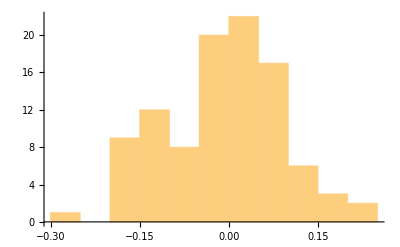

```mathematica
Histogram[Re[M4again], {0.05}]
```

```mathematica
de4again = HistogramDistribution[Re[M4again]];
```

```mathematica
Moment[de4again, 2]
f[4.]/2
```

0.0111333

0.00497359